# Presentation du projet

Classification des Commentaires IMDb avec Régression Logistique

Présentation d’IMDb et de la Base de Données
	IMDb (Internet Movie Database) est une plateforme qui recense des millions de films, séries et documentaires, accompagnés d’avis et de notes laissés par les spectateurs. 
	Grâce à la base de données IMDb disponible sur Kaggle qui contient des commentaires étiqueter positive ou négative, j’ai décidé de mettre en place un algorithme de classification des commentaires en positifs ou négatifs.
	Ainsi, nous pouvons considérer ce projet en 3 grandes étapes qui sont : 
		* Traitement du texte (NLP : Natural Language Processing) : cette étape a pour objectif de nettoyer le texte, de réduire au maximum la dimension et de convertir le texte en vecteur.
		* Mise en place du modèle et test : développer un ou plusieurs modèles et évaluer leur performance et afin de choisir le meilleur.
		*  Mettre en place une zone de saisie ou l’utilisateur poura faire des classifiation de nouveau commentaire.
		
	
Traitement du Texte avec le NLP
	Avant d’entraîner un modèle, il est essentiel de préparer les données textuelles en réduisant leur complexité tout en conservant leur signification. 
	J’ai appliqué des techniques de Traitement Automatique du Langage Naturel (NLP), notamment :
		- Nettoyage des commentaires (suppression des caractères spéciaux, mise en minuscules)
		- Suppression des mots inutiles (stop words)
		- suppression des mots trops rares
		- Vectorisation du texte avec BoW (Bag of Word) pour transformer les mots en données exploitables par le modèle
	Ce prétraitement permet de reduire la dimensionnalité du texte et d’améliorer la performance du modèle.
	
 Entraînement du Modèle de Classification analyse des Résultats
	J’ai choisi d’utiliser un modèle de régression logistique, qui est une méthode de classification binaire. Le modèle a été entraîné sur les données prétraitées et évalué à l’aide de métriques comme :
		- L’exactitude (Accuracy)
		- La précision et le rappel
		- La matrice de confusion pour mieux comprendre ses performances
		

Mise en Place d’une Interface Utilisateur
	Pour rendre ce modèle interactif, j’ai développé une interface simple où les utilisateurs peuvent saisir leur propre commentaire et obtenir une classification automatique (positif ou négatif). 
	Cela permet une expérience utilisateur fluide et une démonstration concrète du modèle.

# Lecture des données

```mathematica
data = Import[StringJoin[{NotebookDirectory[], "\\IMDB_Dataset2.csv"}]];
Dimensions[data]
data[[;;2,;;]]
```

{10000,2}

{{This is one of my all time favorite movies, it's great to watch in groups, I find. It's also great for any Alan Rickman fan, he does such a wonderful job. It's engrossing, entertaining, very surprising... you have to watch it twice, at least. I haven't watched it with anyone who didn't like it or at least find it worthwhile.,positive},{I was pleasantly surprised with this one. It's actually quite interesting and engaging. The cast is strong, even Dan Cortese. Brooke Shields has come into her own as an actress. Black and White must have really set her free, 'cause I have never seen her in this much command playing a conventional character. If marketed right, could be a medium-size hit.,negative}}

Dans cette section, à l' aide de la fonction Import, nous lisons nos données et nous enregistrons dans la variable data. 
Mon ordinateur n' étant pas assez puissant, j' utiliserai juste 5000 lignes de mon dataset . 
J' ai donc fixé ma seed pour être sur de d' avoir le même valeurs car j' utilise des fonctions aléatoires . 
Je sélectionne ensuite 2500 lignes de chaque catégorie, puis je fais un shuffle encore pour m' assurer qu' elles sont répartis de manière aléatoires . 
Puis nous affichons les 2 premières lignes .

# Traitement des données pour reduire la taille du vocabulaire

## Fonction de nettoyage du texte :

```mathematica
(* cette fonction permet de nettoyer le texte en supprimant les stopword, les ponctuation, convertie en minuscule, et fais du stemming*)
cleanData[texte_] := Module[{m},
(*
cette fonction prend en parametre un texte et retourn un texte netoyer : 
exemple : cleanData["i love playing music when i run"]
result : "love plai music run"
*)
m = texte;
m = StringReplace[m,RegularExpression["<[^>]*>"]->""];
m = StringDelete[m, PunctuationCharacter];
m = StringReplace[m,RegularExpression["[^A-Za-z ']"]->""]
(*m = StringJoin[Riffle[Select[StringSplit[m," "],DictionaryWordQ], " "]];*);
m = StringDelete[m,TextCases[m,"ProperNoun"]];
m = ToLowerCase[m];
m = StringSplit[m];
m = DeleteStopwords[m];
m = WordStem[m];
m = Riffle[m, " "];
m = StringJoin[m];
Return[m]
]

(* cette fonction permet de convertir les label(Y) en 0 ou 1*)
boolConvert[text_] := If[text == "positive", 1, 0];

(* applique tous le traitement de texte au data frame*)
appliqueClean[data_] := Table[{cleanData[data[[i, 1]]], boolConvert[data[[i, 2]]]}, {i, 1, Dimensions[data][[1]]}];

(* Combine tous les mot en une chaine (un mot apparait une seul fois), puis cette chaine sera utiliser comme entete pour chaque bacth(portionde traitement) pour le TF-IDF*)
combinedWordsInOne[data_]:=Sort[DeleteDuplicates[StringSplit[StringJoin[Riffle[DeleteDuplicates[data[[All,1]]]," "]]]]]
```

Lors de la prévisualisation des données, nous avons constaté qu' il y avait des valeurs que nous ne voulions pas (les tags html, les chiffres, les symboles, les noms propres, les stops words) . Nous compilons donc toute ces étapes de nettoyage dans la même fonction qui prend un texte en paramètre et retourne le texte nettoyer : 
		- On utilise une expression régulière pour supprimer tous les tags HTML : en utilisant StringReplace et RegularExpression . 
		- Puis on supprime toutes les ponctuations du texte à l' aide StringDelete et PunctuationCharacter (qui correspond aux ponctuations)
     		- Puis on supprime les noms propre grace a StringDelete et TextCases (qui prend un texte et retourne une liste des éléments recherchés dans un texte ex : city, person…etc)
     		- On met tout le texte en minuscule et on le "tokenise", c' est à dire le découper en liste de mot
   		- Puis supprime les stops words avec DeleteSopWords . running = > run)
  		- Après tout cela, nous utilisons StingJoin pour recoller tous nos tokens et retourner une chaîne de caractère . Puis nous créons une fonction qui transforme le positive en 1 et négative en 0 avec un If
  		
 Puis nous combinons ces deux fonctions dans une seule qui s' appel appliqueClean, qui cette fois ci va prendre en paramètre notre dataset (matrice) et retourner la matrice nettoyer . 
 Enfin, je créer une fonction qui va retourner les tokens qui existe (un exemplaire unique de chaque mot) . Cette fonction sera utilisée pour connaître la taille du vocabulaire .

## Applique traitement

```mathematica
(* ici j'applique clean data*)
start = AbsoluteTime[];

data = appliqueClean[data];

end = AbsoluteTime[];
total = end - start
```

561.4165561

```mathematica
Dimensions[data]
```

```mathematica
(*ici j'enregistre le traitement pour gagner du temps plus tard juste en important le fichier*)
Export[StringJoin[{NotebookDirectory[], "\\CleanedIMDBWithOutOnlyEnglishWord2.csv"}], data]
```

E:\thierno\TRAVAIL\S4_403_programmation_haut_niveau\sae\S4.03_Diallo_Thierno\\CleanedIMDBWithOutOnlyEnglishWord2.csv

```mathematica
words = combinedWordsInOne[data];
Length[words]
```

88542

Ici nous appliquons notre fonction appliqueClean à notre base de données, puis mesurons le temps que cela prend . 
Puis nous enregistrons le fichier pour ne plus avoir à refaire le traitement (il est assez couteux en ressource et en temps)
   
A la fin nous regardons pour voir combien de mot différent nous avons . Ici nous constatons que pour nos 10 OOO commentaire nous avons plus de 88 000 mots différent, c' est à dire si nous le convertisseur en matrice en utilisant les algorithme de base tel que BoW (Bag of Word) ou TF - IDF (Term Frequency Inverse Document Frequency) nous aurons une matrice de taille 10 000 x29405. 
Ce qui est très grand, trop grand . Nous allons donc voir comment faire pour réduire la taille du vocabulaire sans trop perdre de données .
Pour cela, nous allons travail sur un echantillon de 4 000 puis apres apliqué notre traitement au 10 000

## Calcul des occurrences des mots pour chaque catégories

## Visualisation des mots (Word Cloud)

Ici, nous allons Nous allons compter l nombre de fois qu' un mot apparaît dans tout le texte, mais également dans les textes positif et négatif. 
Puis nous allons calculer la fréquence qu' un mot soit négative (si proche de 1 = > mot très négatif, si proche de 0 = > mot très positif, si environ 0.5 = > pas tres lien au sentiment) puis mettons tout ça dans un élitiste afin de l' utiliser plus tard. 
Nous allons également afficher un nuage de mots pour voir rapidement lesquelles apparaissent le plus de fois et également voir les différences principales entre nos deux classes .

```mathematica
(* chargement des données enregistrer pour gagner du temps(donc shuffle)*)
data = Import[StringJoin[{NotebookDirectory[], "\\CleanedIMDBWithOutOnlyEnglishWord2.csv"}]];
SeedRandom[1234];  (*pour povoir comparer mes modeles sur les memes données*)
nRowByClass = 2000;
pos = Select[data, Function[{row}, row[[2]]==1]];
neg = Select[data, Function[{row}, row[[2]]==0]];
data = RandomSample[Join[RandomSample[pos, nRowByClass], RandomSample[neg, nRowByClass]]];
data[[;;2, ;;]]

words = combinedWordsInOne[data];
```

{{wife watch dvring encor action past week worst horror flick seen predict dialogu wife guess line spoken hokei special effect screenplai drift place think annoi stereotyp variou charact plot mention gratuit sex scene young heroin movi neither real purpos bare certain part anatomi camera movi categor comedi horror villain movi spider stop motion anim believ cant sai better job make film amateurish wasnt b movi closer d movi f possibl think fiction pass,0},{movi wasnt bad compar sequel origin direct th fame act bad inde gore special effect help make interest that thing like scream make effect artist film effect offthewal bizarr watch bad movi just crazi theyr gonna movi isnt realli gori extrem nasti eyeballmunch scene middl involv toi maggot make guest appear probabl wasnt enthusiast need monei time possibl like weirdo th instal favorit youll probabl like like better,0}}

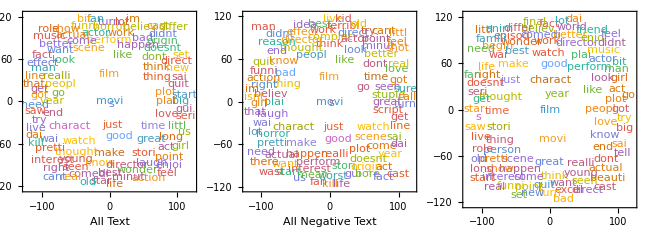

```mathematica
all = Counts[StringSplit[StringJoin[Riffle[data[[All,1]]," "]]]];
allList = Lookup[all, words, 0];

neg = Select[data, #[[2]] == 0&] ;
allNeg = Counts[StringSplit[StringJoin[Riffle[neg[[All,1]]," "]]]];
allNegList = Lookup[allNeg, words, 0];

pos = Select[data, #[[2]] == 1&] ;
allPos = Counts[StringSplit[StringJoin[Riffle[pos[[All,1]]," "]]]];
allPosList = Lookup[allPos, words, 0];

freqWord = allNegList / allList (* si proche de 1 => mot tres negatif, si proche de 0 => mot tres positif, si environ 0.5 => pas tres lien au sentiment*);

nbMotParType = Transpose[{words, allList, allNegList, allPosList, freqWord}];

GraphicsRow[{
WordCloud[all, Frame->True, FrameLabel->Style["All Text", Bold, 14]],
WordCloud[allNeg, Frame->True, FrameLabel->Style["All Negative Text", Bold, 14]],
WordCloud[allPos, Frame->True, FrameLabel->Style["All Positive Text", Bold, 14]]
}]
```

Ces  trois nuages de mots présente  le vocabulaire utilisé dans les critiques de films . 
Le premier, à gauche, regroupe tous les avis confondus, mettant en avant des termes généraux comme "film", "movie", "like", "make", "character", "scene" et "watch", qui sont fréquemment utilisés pour parler de cinéma . 
Le deuxième, au centre, se concentre sur les critiques négatives, où apparaissent des mots comme "bad", "boring", "waste", "stupid", "worst" et "dull", reflétant des jugements négatifs et des frustrations . 
Enfin, le troisième, à droite, affiche le vocabulaire des critiques positives, dominé par des termes valorisants tels que "love", "best", "great", "amazing", "enjoy", "fun" et "perfect", exprimant une appréciation enthousiaste . 
Cette comparaison montre clairement qu’il y’a une différence dans le vocabulaire des commentaire positif et négatif et qu’il y’a des mot en commun, qui porte géneralement sur le thème.

## Visualisation des mots (Nuage de point et histogramme des fréquences)

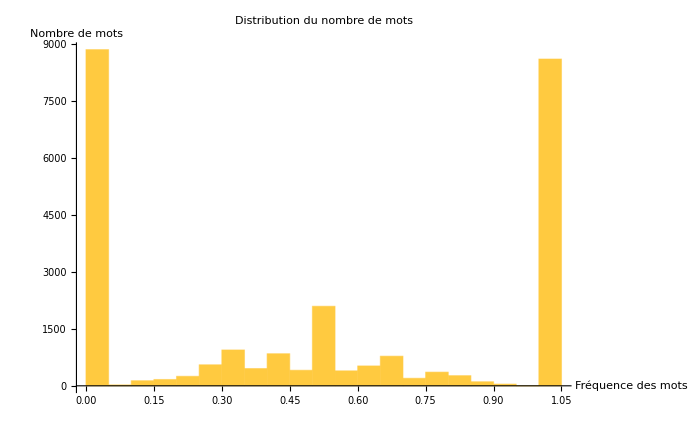

```mathematica
(*histogram des frequence*)
Histogram[nbMotParType[[All, 5]], AxesLabel->{"Fréquence des mots","Nombre de mots"}, PlotLabel-> Style["Distribution du nombre de mots", Bold, 18]]
```

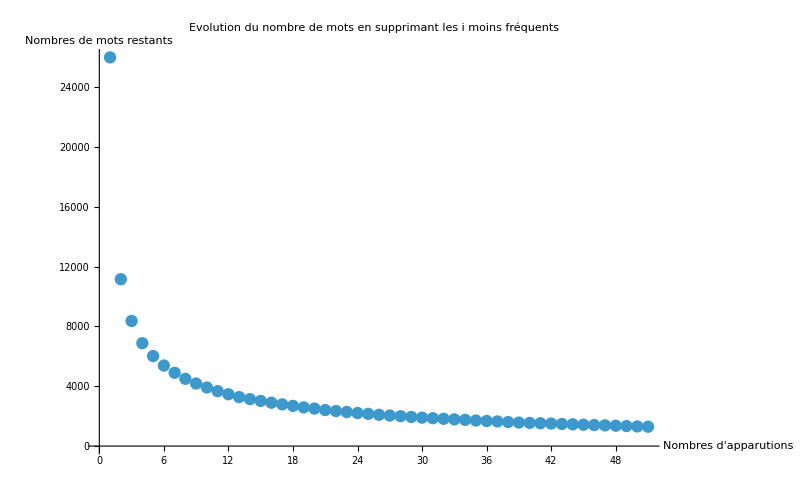

3671

```mathematica
(*Calcul du nombre de mot restant si on supprime les plus rares*)
ListPlot[Table[Length[Select[nbMotParType, #[[2]] >  i &]], {i, 0, 50}], PlotRange->Full, AxesLabel-> {"Nombres d'apparutions", "Nombres de mots restants"}, PlotLabel->Style["Evolution du nombre de mots en supprimant les i moins fréquents", Bold, 18]]

(* suppresion des mot qui apparaisse moins de 10 fois sur nos 5000 commentaire, ils sont probablement inutile *)
nbMotParType2 = Select[nbMotParType, #[[2]] > 10 &];
Length[nbMotParType2]
```

Le graphique en bar montre que nous avons environ 20000 mots qui apparaissent qu’une seule fois dans le texte dans si c’est apparaître qu’une seule fois dans tout notre corpus de 5000 commentaires cela veut dire qu’ils sont probablement pas très importants pour faire la différence entre commentaires positifs et commentaires négatifs on constate également qu’il y a autour de 3000 mots qui ont une fréquence de 0.5, ce qui signifie qu’il apparaissent autant de fois dans les commentaires positif que dans les négatifs. 
Et les autres mots sont un petit peu plus rares par rapport à ces 2 catégories seront donc ce qui nous permettront de différencier commentaire positif et négatif. 
Ce nuage de point nous présente le nombre de mots qu’il me reste( en ordonnée) si nous supprimons les mots qui apparaissent moins de “N” fois (en abscisse).
En supprimant tous les mots qui apparaissent juste une fois il nous reste environ 15000 mots, c’est à dire que nous avons pu diviser notre corpus par 2 (environ)
En continuant sur cette logique, nous constatons également que quand nous supprimons les mots qui apparaisse moins de 10 fois il nous reste plus qu’environ 4500 mots 
En partant du principe qu’un mots apparaît soit dans un texte négatif soit dans un texte positif on peut raisonner comme suit
Un mot qui apparaît moins de 10 fois, cela signifie qu’il apparaît dans moins de 0,4% de nos commentaires(positif|négatif). Je conclu donc qu’il n’est pas essentiel pour faire la différence entre texte positif et négatif.
Je décide donc de supprimer tous les mots qui apparaissent moins de 10 fois
On se retrouve donc avec un vocabulaire de 4254 mots (qui peux etre réduit ou utiliser pour entrainer notre modèle).

## Traitement en plus a comparer avec le traitement de base

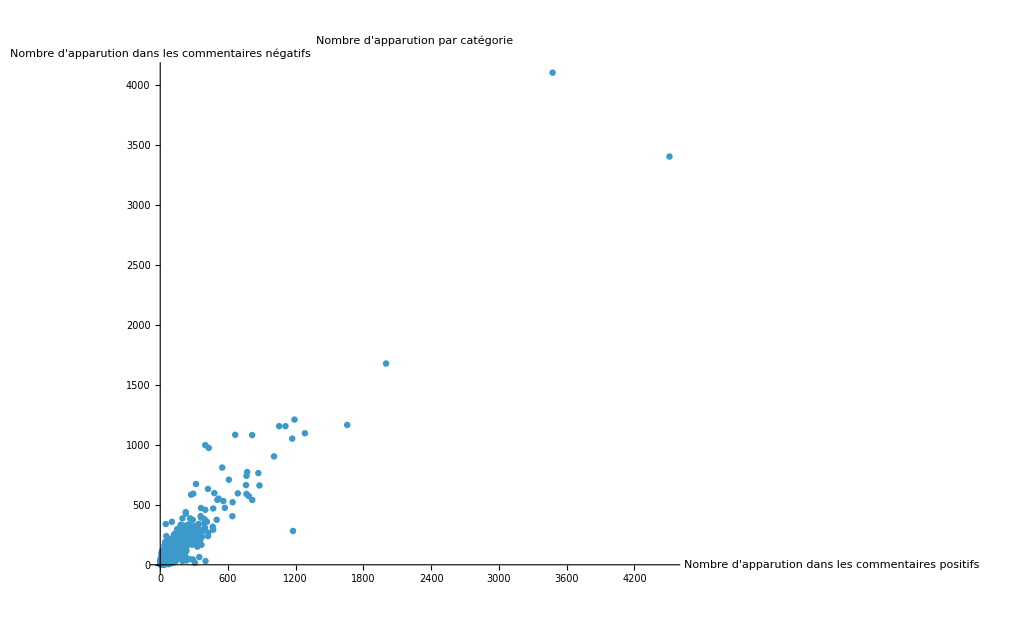

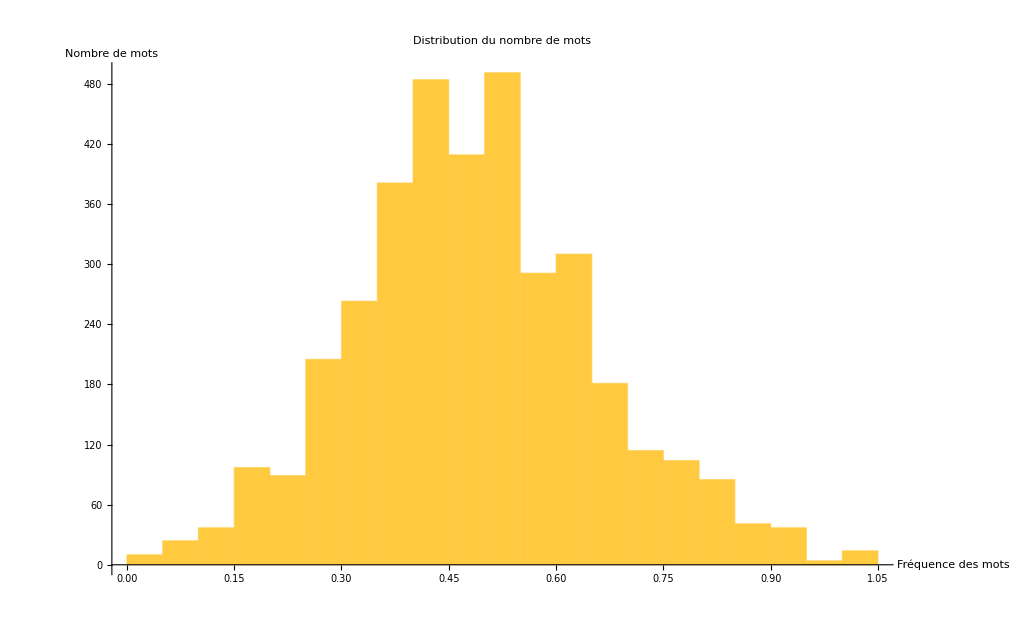

```mathematica
ListPlot[nbMotParType2[[All, 3;;4]], PlotRange->Full, AxesLabel->{"Nombre d'apparution dans les commentaires positifs","Nombre d'apparution dans les commentaires négatifs"}, PlotLabel-> Style["Nombre d'apparution par catégorie", Bold, 18]]
(*histogram des frequence*)
Histogram[nbMotParType2[[All, 5]],  AxesLabel->{"Fréquence des mots","Nombre de mots"}, PlotLabel-> Style["Distribution du nombre de mots", Bold, 18]]
```

Ici, nous constatons qu’il y a des mots qui apparaissent énormément (comme film et movi). 
Mais nous constatons également qu’il y a de nombreux mots qui apparaissent autant de fois dans les texte positif et négatif, la logique voudrait que s’ il apparaît autant de fois dans les deux catégorie, c’est que ce sont des mots neutre ou avec un sentiment assez faible. Nous allons supprimer donc ces mots et entraîner un deuxième modèle et voir si celui-ci est plus performant ou pas.

```mathematica
(* ici on va commencer par observé et|ou pas drop les point qui on un nbNeg > 2000 et nbPos > 1000 car sur le scatter plot, on voit qu'il n'apport rien de plus*)
observe = Select[nbMotParType2, #[[3]] > 2000 && #[[4]] > 1000 &];
observe
```

{{film,7576,3475,4101,3475/7576},{movi,7912,4510,3402,2255/3956}}

```mathematica
(*Nous allons conserver les mot suivant: just, like*)
```

```mathematica
(* ici on va commencer par observé et|ou pas drop les point qui on un nbNeg > 13000 et nbPos > 12000 car sur le scatter plot, on voit qu'il n'apport rien de plus*)
nbMotParType3 = Select[nbMotParType2, #[[1]]  != "movi" ||  #[[1]]  != "film" &];
Length[nbMotParType3]
```

3671

83

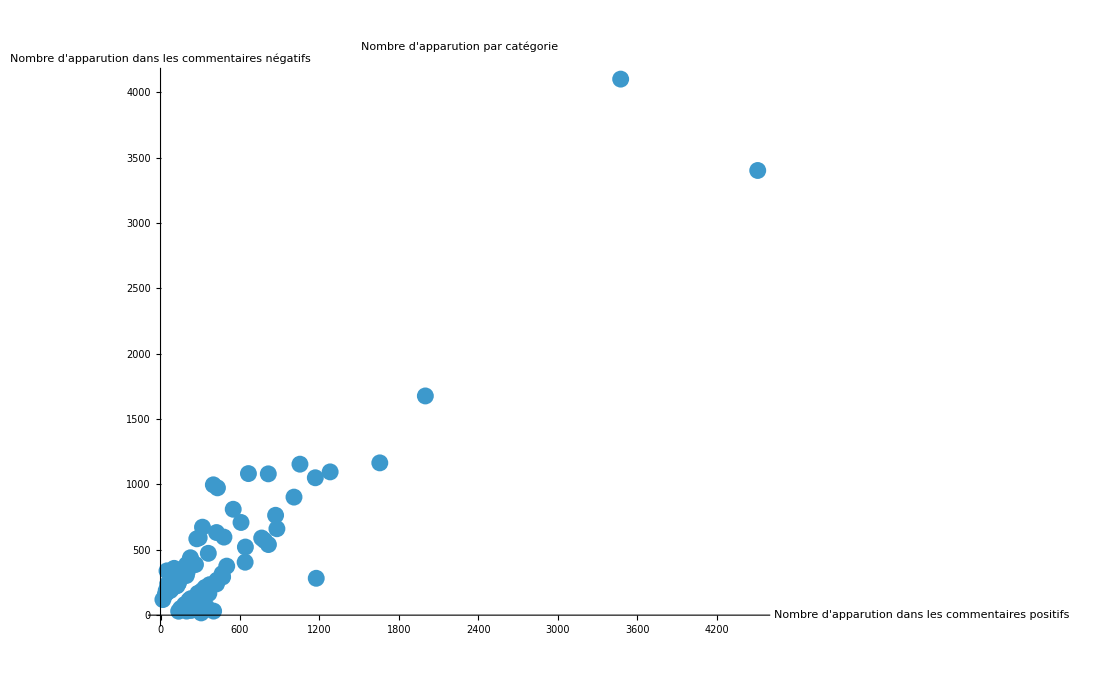

```mathematica
(* ici on va supprimer tous les mot qui se trouve a +|-50 de la droite y=x (dans la diagonale, car il apparaisse autant de fois dans les negatif que les positif.)*)
param = 100;
nbMotParType4 = Select[nbMotParType3, Abs[#[[3]] - #[[4]]] >= param &];
Length[nbMotParType4]
ListPlot[nbMotParType4[[All, 3;;4]], PlotRange->Full, AxesLabel->{"Nombre d'apparution dans les commentaires positifs","Nombre d'apparution dans les commentaires négatifs"}, PlotLabel-> Style["Nombre d'apparution par catégorie", Bold, 18]]
```

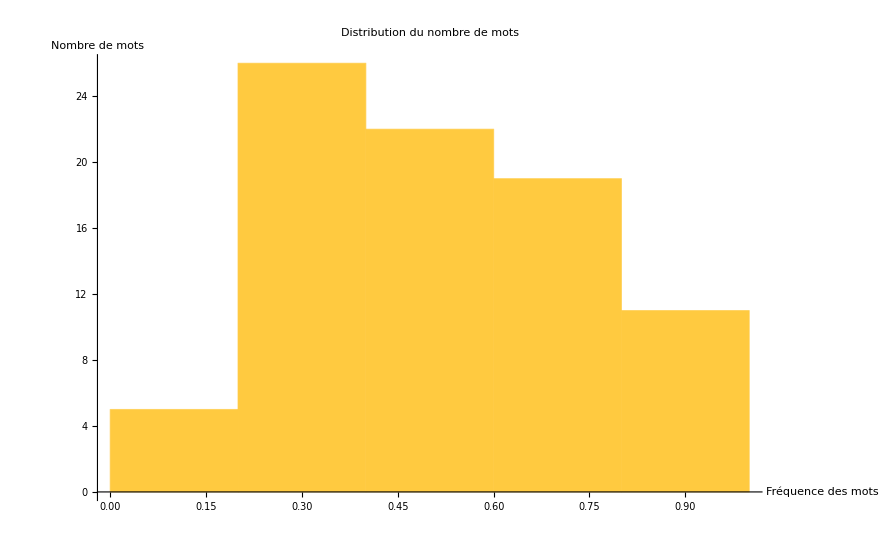

```mathematica
Histogram[nbMotParType4[[All, 5]],  AxesLabel->{"Fréquence des mots","Nombre de mots"}, PlotLabel-> Style["Distribution du nombre de mots", Bold, 18]]
```

On se rend compte qu’en supprimant ces mots, nous supprimons une très grande partie de notre vocabulaire. 
Maintenant nous allons entraîner deux modèles. L’un avec le vocabulaire  de 4000 mots et l’autre d’environ 100 mots et voir quel est le plus performant et si le fait d’avoir plus de mot augmente la performance de notre modèle et notre théorie est vrai.

# Transformation du text en vecteur

## Définition des fonction

Dans cette partie nous allons définir 2 fonctions.
Une fonction qui va prendre en paramètre un une matrice et un vocabulaire et qui va retourner une matrice qui a la place du texte, contient le nombre d’occurence de chaque mots (dans l’ordre du vocabulaire). Cette fonction nous permet donc de convertir notre texte en vecteur.
Puis nous allons définir process ByPartBoW qui va prendre en paramètre une matrice, et le nombre d’élément que l’on souhaite traiter par lot, puis va diviser la la matrice en sous matrice de n élément et va appliqué BoW, nous faisons cela pour permettre à l’ordinateur de traiter de grand fichier.
nous avons utilisé Reap et Sow pour éviter que à chaque tour de boucle on ajoute à nos données qui ont déjà été traité les nouvelles données, car nous cela nous crée une variable qui est extrêmement lourde et qui fait planter la machine donc en utilisant Sow(semer dans plusieur espace mémoire sans pour autant les connaître) et Reap(recueillir les données semer) nous les enregistres dans un espace mémoire de manière séparée et nous les récupérons plus tard à la fin du traitement et les retournons.

```mathematica
(*Transforme le texte en vecteur en utilisant BoW*)
bagOfWordExtractors[data_, vocabulaire_] := Module[{}, 
Table[{Lookup[Counts[TextWords[data[[i, 1]]]], vocabulaire, 0], data[[i, 2]]}, {i, 1, Length[data]}]
]

(*ici on utilise Bag of Word*)
processesByPartBoW[data_, nbBatch_, vocabulaire_] := Module[{df = {}, batch, n},
batch = Partition[data, nbBatch, nbBatch,1,{}];
n = Dimensions[batch][[1]];
Flatten[Reap[
For[i=1, i <= n, i++, 
Sow[bagOfWordExtractors[batch[[i]], vocabulaire]];
Print["avancement : ", i, "/", n]
];
][[2, 1]], 1]
]
```

## Conversion

Ici nous convertissons notre texte en vecteur en utilisant BoW (Bag of Word)

```mathematica
(*recuperation juste des mot selectionnée (juste traitement de base + suppression des mots qui apparaisse moins de 10 fois) *)
mots1 = nbMotParType2[[All, 1]];

df1 = processesByPartBoW[data, 1000, mots1];
```

avancement : 1/4

avancement : 2/4

avancement : 3/4

avancement : 4/4

```mathematica
(*recuperation juste des mot selectionnée (traitement de base + suppression des mots qui apparaisse moins de 10 fois + suppression des mot de la diagonale ) *)
mots2 = nbMotParType4[[All, 1]];

df2 = processesByPartBoW[data, 1000, mots2];
```

avancement : 1/4

avancement : 2/4

avancement : 3/4

avancement : 4/4

# Classification

## Définition de fonction

Regression logistique
La régression logistique est un algorithme d’apprentissage supervisé utilisé pour la classification binaire. La régression logistique applique la fonction sigmoïde pour transformer la sortie en une probabilité entre 0 et 1.

La fonction sigmoïde est définie comme suit :  ou on a  avec X qui est la matrice de nos paramètres, w les poids de notre modèle et b le biais du modèle.
L’objectif est d’entraîner un modèle pour trouver les poids optimaux permettant de prédire la classe d’une donnée donnée en fonction de ses caractéristiques.

Fonction Coût(Log de vraisemblance)
Un peu comme la fonction coût d’une régression linéaire classique(Erreur quadratique moyenne), le log de vraisemblance calcule l’erreur entre les prédictions et les valeurs réelles elle est définie par :  ou y représente les valeurs réelles des labels, 𝑦 chapeau (ou yPred) est la prédiction du modèle, et 𝑚 est le nombre d’exemples. Cette fonction est utilisée pour mesurer la qualité du modèle, un score plus faible indique de meilleures prédictions.

Fonctionnement de la descent de gradient
Pour entrainer notre modèle, nous allons utiliser la descente de gradient est une methode d’optimisation utilisée pour ajuster les paramètres d’un modèle afin de minimiser une fonction de coût. Le principe est le suivant : On dérive la fonction de coût par rapport aux paramètres (poids et biais) pour obtenir la direction de pente. Puis on ajuste les poids 𝑤 et le biais 𝑏 dans la direction opposée au gradient pour descendre vers le minimum, donc  on a  et  où α (learning rate) est un facteur d’apprentissage qui contrôle la taille des mises à jour. Enfin on répète ces mises à jour jusqu’à atteindre un minimum local ou global de la fonction de coût.

-Graphics-

```mathematica
(*log de vraisemblance *)
fonctionCout[y_, yPred_] := Module[{m, loss}, 
m=Length[y];
loss = -(1/m)*Total[y*Log[yPred]+(1-y)*Log[1-yPred]];
Return[loss]
];

logisticRegressionFit[data_,labels_,epochs_:100,learningRate_:0.3]:=Module[
{m,n,weights,bias,dw,db,linearModel,yPred, evolutionError = {}},
{m,n}=Dimensions[data];
weights=ConstantArray[0,n];
bias=0;

(*Boucle d'entraînement*)
Do[linearModel=data.weights+bias;
yPred=LogisticSigmoid[linearModel];
AppendTo[evolutionError, fonctionCout[labels, yPred]] ;

(*Calcul du gradient*)
dw=(1/m)* Transpose[data].(yPred-labels);
db=(1/m)* Total[yPred-labels];

(*Mise à jour des poids*)

(*Mise à jour des poids et biais*)
weights-=learningRate*dw;
bias-=learningRate*db;,
{epochs}];
(*Retourner les paramètres entraînés*)
<|"weights"->weights,"bias"->bias, "EvolutionError" -> evolutionError|>
]

predictClass[vec_, weights_, bias_] := Module[{result},
result = vec.weights + bias;
result = LogisticSigmoid[result];
Return[result];
]
```

## Divise dataset fonction

Cette fonction va nous permettre de séparer notre dataset en trainset et testset selon un ratio qu’ on indiquera en paramètre. elle va d’abord  melanger le dataset avant de le séparer pour s’assurer que les données sont distribuer de manière aléatoire.

```mathematica
(* permet de diviser mon dataset en train set et test set en fonction d'un ratio *)
SplitDataset[data_,trainRatio_:0.8]:=Module[{shuffledData,splitIndex,trainSet,testSet},
shuffledData=RandomSample[data];
(*Déterminer l'index de coupure basé sur le ratio donné*)
splitIndex=Floor[trainRatio Length[data]];
(*Séparer les données *)
trainSet=Take[shuffledData,splitIndex];
testSet=Drop[shuffledData,splitIndex];
{trainSet,testSet}
]
```

## entrainement

## entrainement sur df1 (traitement de base)

Nous allons commencer l’entraînement de notre modèle 1 (celui avec 4000 mots). Nous allons chercher quel est le meilleur learning rate pour ce modèle.

```mathematica
(* entrainement sur df1 (peut de traitement )*)
{traindf1, testdf1} = SplitDataset[df1];
Xdf1 = traindf1[[;;,1]];
Ydf1 = traindf1[[;;, 2]];
```

```mathematica
x = Table[logisticRegressionFit[Xdf1, Ydf1, 100, i], {i, 0.1 , 0.9, 0.1}];
```

learning rate : 0.1

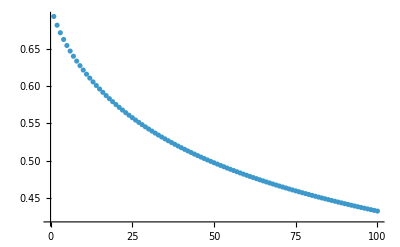

learning rate : 0.2

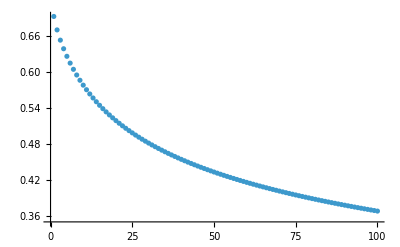

learning rate : 0.3

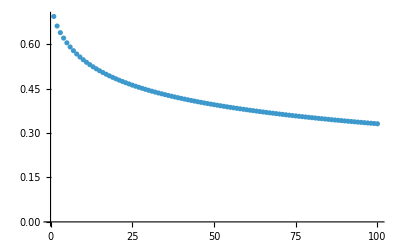

learning rate : 0.4

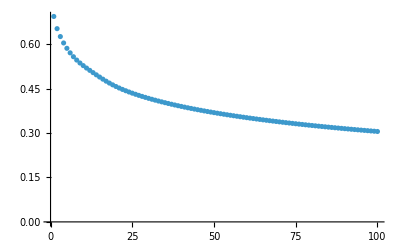

learning rate : 0.5

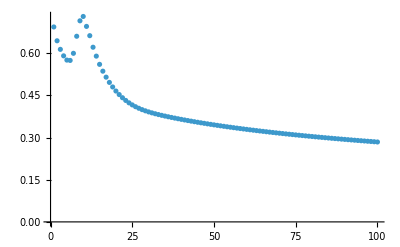

learning rate : 0.6

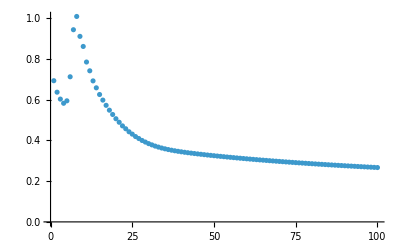

learning rate : 0.7

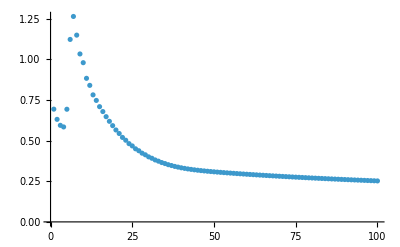

learning rate : 0.8

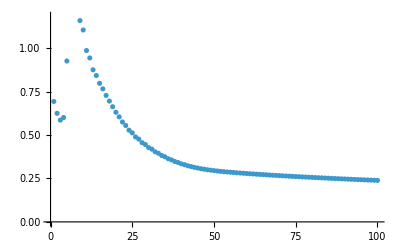

learning rate : 0.9

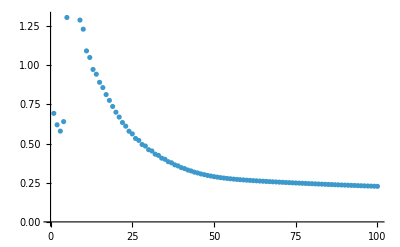

```mathematica
Do[
Print["learning rate : ", N[i / 10]];.08
Print[ ListPlot[x[[i]]["EvolutionError"]] ]
, {i, 1, 9}]
```

Ici nous constatons que le meilleur learning rate est celui de 0.9, il nous permet de baisser rapidement notre fonction coût . 
Maintenant, nous allons lancer un entrainement avec 500 (je suis limité par mon matériel)  itération pour voir si il converge vraiment.

```mathematica
model1 = logisticRegressionFit[Xdf1, Ydf1, 500, 0.9];
```

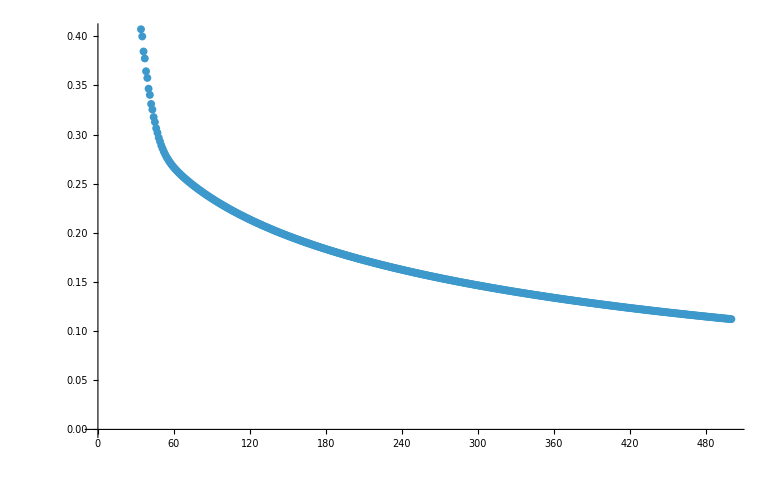

```mathematica
ListPlot[model1["EvolutionError"]]
```

Nous constatons que notre modèle converge toujour pour un leaning rate de 0.9 . Nous allons donc utiliser le modeèle 1 avec les parametre suivant : LearningRate = 0.9 et Iteration = 500.
Nous constatons aussi que notre modèle commence à stagner(legèrement : perte de 0,01 par la lost fonction en 50 itération), ce qui signifie qu’on a pas besoin de l’entraîner plus longtemps, car  le gain sera négligeable.

## Entrainement modèle avec df2 (mot très reduit)

Nous allons commencer l' entraînement de notre modèle 2 (celui avec 200 mots) . Nous allons chercher quel est le meilleur learning rate pour ce modèle .

```mathematica
(* entrainement sur df1 (peut de traitement )*)
{traindf2, testdf2} = SplitDataset[df2];
Xdf2 = traindf2[[;;,1]];
Ydf2 = traindf2[[;;, 2]];
```

Learning rate : 0.1

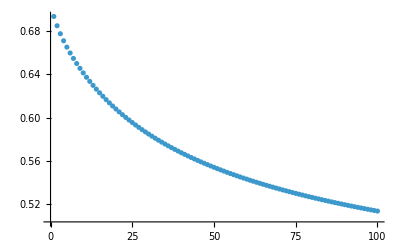

Learning rate : 0.2

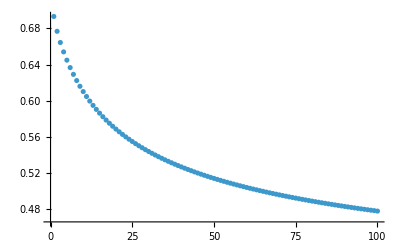

Learning rate : 0.3

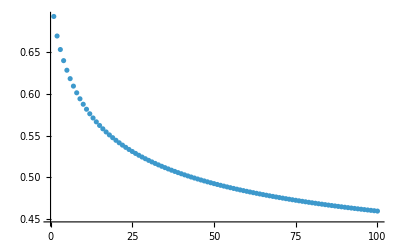

Learning rate : 0.4

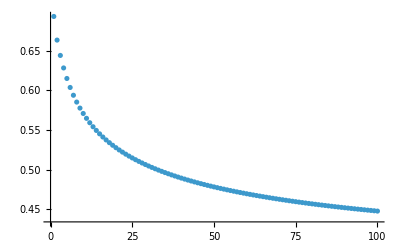

Learning rate : 0.5

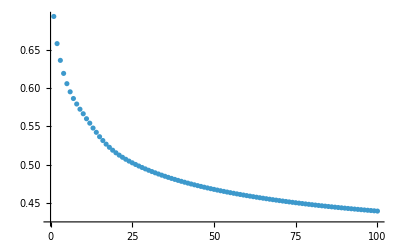

Learning rate : 0.6

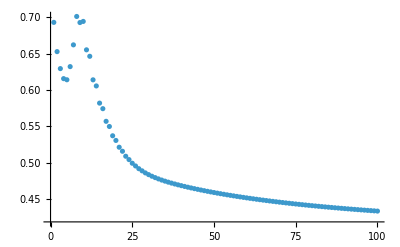

Learning rate : 0.7

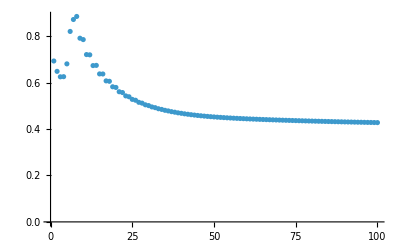

Learning rate : 0.8

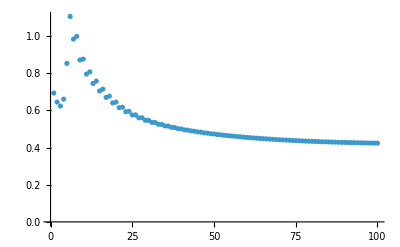

Learning rate : 0.9

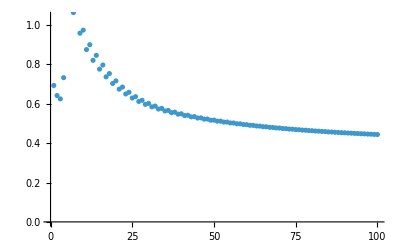

```mathematica
x = Table[logisticRegressionFit[Xdf2, Ydf2, 100, i]["EvolutionError"], {i, 0.1, 0.9, 0.1}];
For[i = 1, i <= Length[x], i++, 
Print["Learning rate : ", N[i/10]];
Print[ ListPlot[x[[i]]]]
]
```

Ici nous constatons que le meilleur learning rate est celui de 0.9, il nous permet de baisser rapidement notre fonction coût . 
  Maintenant, nous allons lancer un entrainement avec 500 puis 1000 puisqu’il a moins de paramètre (je suis imité par mon matériel)  itération pour voir si il converge vraiment .

```mathematica
modeldf2 = logisticRegressionFit[Xdf2, Ydf2, 1000, 0.9];
```

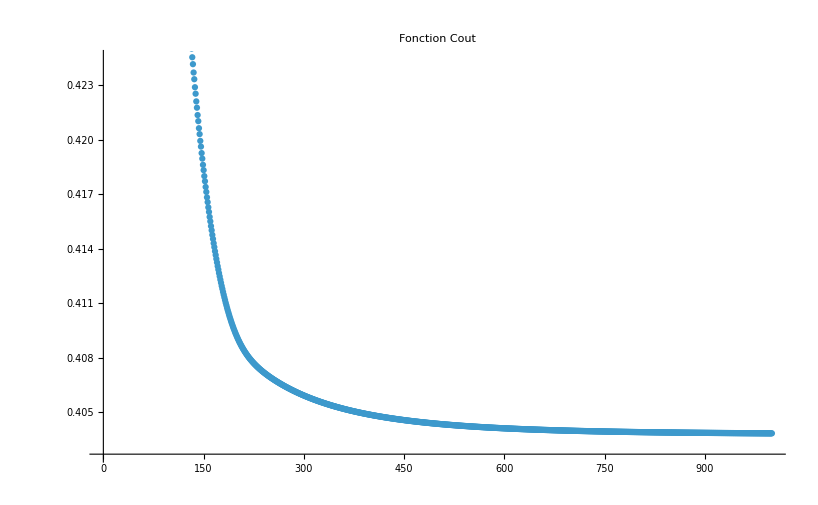

```mathematica
ListPlot[modeldf2["EvolutionError"], PlotLabel-> Style["Fonction Cout", Bold, 18]]
```

Nous constatons que notre modèle converge toujour pour un leaning rate de 0.9 . Nous allons donc utiliser le modeèle 1 avec les parametre suivant : LearningRate = 0.9 et Iteration = 500.
Nous constatons aussi que notre modèle commence à stagner, ce qui signifie qu' on a pas besoin de l' entraîner plus longtemps, car le gain sera négligeable .

Nous avons maintenant deux modèle en notre possession, nous allons comparer leurs performances .

# Test de la classification

## Définition fonction

```mathematica
(*retourne la matrice de confusion par rapport a un seuil donnée*)
confusionMatrix[y_, prob_, seuil_] := Module[{pred, TP = 0, TN =0, FP =0, FN =0},
pred = Table[If[prob[[i]] >= seuil, 1, 0], {i, 1, Dimensions[prob][[1]]}];

TP=Count[Transpose[{y,pred}],{1,1}];
TN=Count[Transpose[{y,pred}],{0,0}];
FP=Count[Transpose[{y,pred}],{0,1}];
FN=Count[Transpose[{y,pred}],{1,0}];

(*Retourner les résultats sous forme d'association*)
<|"TP"->TP,"TN"->TN,"FP"->FP,"FN"->FN|>
];

(* retourne la accuracy pour un seuil donnée *)
accuracy[y_, prob_, seuil_] := Module[{confuseMatrix = confusionMatrix[y, prob, seuil], acc}, 
acc = (confuseMatrix["TP"] + confuseMatrix["TN"]) / Dimensions[y][[1]];
Return[acc];
];

(*retourne la liste des points pour la ROCCurve *)
ROCCurve[y_, prob_, step_] := Table[
{
confusionMatrix[y, prob, i]["FP"] / (confusionMatrix[y, prob, i]["FP"] + confusionMatrix[y, prob, i]["TN"]),
confusionMatrix[y, prob, i]["TP"] / (confusionMatrix[y, prob, i]["TP"] + confusionMatrix[y, prob, i]["FN"])
},{i, 0, 1, step}];

precision[y_, prob_, seuil_] := Module[{confuseMatrix = confusionMatrix[y, prob, seuil], pre}, 
pre = confuseMatrix["TP"] / (confuseMatrix["TP"] + confuseMatrix["FP"]);
Return[pre];
];

recall[y_, prob_, seuil_] := Module[{confuseMatrix = confusionMatrix[y, prob, seuil], rec}, 
rec = confuseMatrix["TP"] / (confuseMatrix["TP"] + confuseMatrix["FN"]);
Return[rec];
];

F1Score[y_, prob_, seuil_] := 2* ((precision[y, prob, seuil] * recall[y, prob, seuil]) / (precision[y, prob, seuil] + recall[y, prob, seuil]) )
```

## Test sur les données d’entrainement

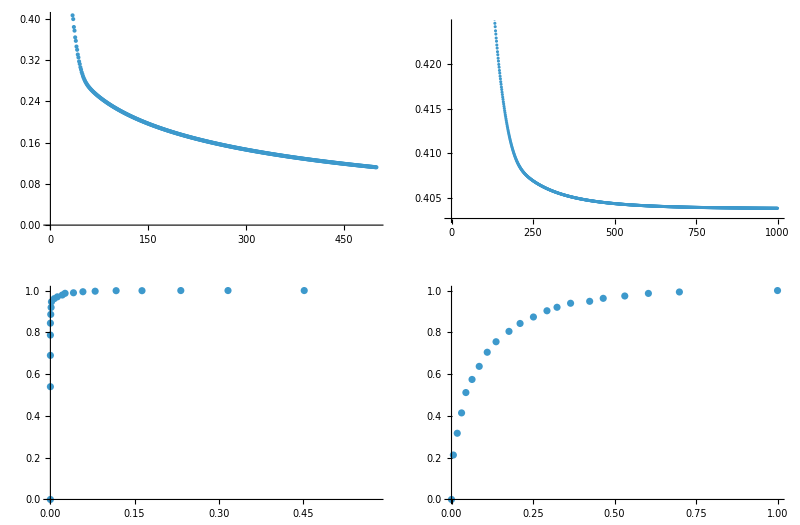

```mathematica
i = 0.5 ;
X1 = traindf1[[All, 1]];
Y1 = traindf1[[All, 2]];
X2 = traindf2[[All, 1]];
Y2 = traindf2[[All, 2]];
Y1pred = predictClass[X1, model1["weights"], model1["bias"]];
Y2pred = predictClass[X2, modeldf2["weights"], modeldf2["bias"]];


acc1 = accuracy[Y1, Y1pred, i];
acc2 = accuracy[Y2, Y2pred, i];

confMatrix1 = confusionMatrix[Y1, Y1pred, i];
confMatrix1 = {
{"Predit \\ Réel","Positive","Négative"},
{"Positive",confMatrix1["TP"],confMatrix1["FP"]},
{"Négative",confMatrix1["FN"],confMatrix1["TN"]}
};
confMatrix2 = confusionMatrix[Y2, Y2pred, i];
confMatrix2 = {
{"Predit \\ Réel","Positive","Négative"},
{"Positive",confMatrix2["TP"],confMatrix2["FP"]},
{"Négative",confMatrix2["FN"],confMatrix2["TN"]}
};

confMatrix1 = Grid[confMatrix1,Frame->All,Alignment->Center ,Spacings->{2,2},Background->{{LightGray},{LightGray}}];
confMatrix2 = Grid[confMatrix2,Frame->All,Alignment->Center ,Spacings->{2,2},Background->{{LightGray},{LightGray}}];

pre1 = precision[Y1, Y1pred, i];
pre2 = precision[Y2, Y2pred, i];

rec1 = recall[Y1, Y1pred, i];
rec2 = recall[Y2, Y2pred, i];

F1S1 = F1Score[Y1, Y1pred, i];
F1S2 = F1Score[Y2, Y2pred, i];

roc1 = ROCCurve[Y1, Y1pred, 0.05];
roc2 = ROCCurve[Y2, Y2pred, 0.05];

evolErr1 = model1["EvolutionError"];
evolErr2 = modeldf2["EvolutionError"];

GraphicsGrid[
{
{Style["Modèle 1 : grand corpus", FontSize->17, FontWeight->Bold], Style["Modèle 2 : faible corpus", FontSize->17, FontWeight->Bold]},
{"Vitesse d'entrainement M1", "Vitesse d'entrainement M2"},
{ListPlot[evolErr1], ListPlot[evolErr2]},
{"ROC curve M1", "ROC curve M2"},
{ListPlot[roc1], ListPlot[roc2]},
{"Matrice de confusion M1", "Matrice de confusion M2"},
{confMatrix1, confMatrix2},
{"\n Accuracy M1",  "\n Accuracy M2"},
{Style[N[acc1], FontSize->14, FontWeight->Bold],  Style[N[acc2], FontSize->14, FontWeight->Bold]}, 
{"\n Précision M1", "\n Précision M2"},
{Style[N[pre1], FontSize->14, FontWeight->Bold],  Style[N[pre2], FontSize->14, FontWeight->Bold]},
{"\n Recall M1", "\n Recall M2"},
{Style[N[rec1], FontSize->14, FontWeight->Bold],  Style[N[rec2], FontSize->14, FontWeight->Bold]}, 
{"\n F1 Score M1", "\n F1 Score M2"},
{Style[N[F1S1], FontSize->14, FontWeight->Bold],  Style[N[F1S2], FontSize->14, FontWeight->Bold]}
}, 
Spacings->{2,5},
Alignment->{Center,Center}
]
```

Le Modèle 1, entraîné sur un grand corpus, présente des performances remarquables . La courbe d' entraînement montre une diminution régulière de la perte, indiquant un apprentissage stable et efficace . Les métriques de performance (accuracy, précision, rappel et F1 score) avoisinent toutes les 98 %, ce qui reflète une excellente capacité de généralisation sur le train set . La matrice de confusion révèle très peu d' erreurs (34 faux positifs et 34 faux négatifs), tandis que la courbe ROC démontre une excellente capacité de séparation entre les classes .

À l' inverse, le Modèle 2, basé sur un corpus réduit, montre des performances nettement inférieures . La perte d' entraînement diminue rapidement au début mais tend à stagner, indiquant un apprentissage moins robuste . Avec une précision de 80 %, un rappel de 84 % et un F1 score de 82 %, il est clair que le modèle commet davantage d' erreurs, comme le confirme la matrice de confusion (334 faux positifs et 254 faux négatifs) . La courbe ROC moins prononcée témoigne aussi d' une capacité de discrimination réduite . En résumé, la quantité de données d' entraînement a un impact majeur sur la qualité du modèle .

## Test sur de nouvelle données

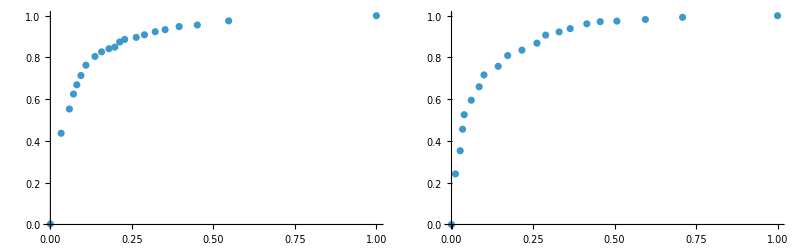

```mathematica
i = 0.5 ;
X1 = testdf1[[All, 1]];
Y1 = testdf1[[All, 2]];
X2 = testdf2[[All, 1]];
Y2 = testdf2[[All, 2]];
Y1pred = predictClass[X1, model1["weights"], model1["bias"]];
Y2pred = predictClass[X2, modeldf2["weights"], modeldf2["bias"]];


acc1 = accuracy[Y1, Y1pred, i];
acc2 = accuracy[Y2, Y2pred, i];

confMatrix1 = confusionMatrix[Y1, Y1pred, i];
confMatrix1 = {
{"Predit \\ Réel","Positive","Négative"},
{"Positive",confMatrix1["TP"],confMatrix1["FP"]},
{"Négative",confMatrix1["FN"],confMatrix1["TN"]}
};
confMatrix2 = confusionMatrix[Y2, Y2pred, i];
confMatrix2 = {
{"Predit \\ Réel","Positive","Négative"},
{"Positive",confMatrix2["TP"],confMatrix2["FP"]},
{"Négative",confMatrix2["FN"],confMatrix2["TN"]}
};

confMatrix1 = Grid[confMatrix1,Frame->All,Alignment->Center ,Spacings->{2,2},Background->{{LightGray},{LightGray}}];
confMatrix2 = Grid[confMatrix2,Frame->All,Alignment->Center ,Spacings->{2,2},Background->{{LightGray},{LightGray}}];

pre1 = precision[Y1, Y1pred, i];
pre2 = precision[Y2, Y2pred, i];

rec1 = recall[Y1, Y1pred, i];
rec2 = recall[Y2, Y2pred, i];

F1S1 = F1Score[Y1, Y1pred, i];
F1S2 = F1Score[Y2, Y2pred, i];

roc1 = ROCCurve[Y1, Y1pred, 0.05];
roc2 = ROCCurve[Y2, Y2pred, 0.05];


GraphicsGrid[
{
{Style["Modèle 1 : grand corpus", FontSize->17, FontWeight->Bold], Style["Modèle 2 : faible corpus", FontSize->17, FontWeight->Bold]},
{"ROC curve M1", "ROC curve M2"},
{ListPlot[roc1], ListPlot[roc2]},
{"Matrice de confusion M1", "Matrice de confusion M2"},
{confMatrix1, confMatrix2},
{"\n Accuracy M1",  "\n Accuracy M2"},
{Style[N[acc1], FontSize->14, FontWeight->Bold],  Style[N[acc2], FontSize->14, FontWeight->Bold]}, 
{"\n Précision M1", "\n Précision M2"},
{Style[N[pre1], FontSize->14, FontWeight->Bold],  Style[N[pre2], FontSize->14, FontWeight->Bold]},
{"\n Recall M1", "\n Recall M2"},
{Style[N[rec1], FontSize->14, FontWeight->Bold],  Style[N[rec2], FontSize->14, FontWeight->Bold]}, 
{"\n F1 Score M1", "\n F1 Score M2"},
{Style[N[F1S1], FontSize->14, FontWeight->Bold],  Style[N[F1S2], FontSize->14, FontWeight->Bold]}
}, 
Spacings->{2,5},
Alignment->{Center,Center}
]
```

Sur le jeu de test, on observe que le Modèle 1, bien qu' entraîné sur un grand corpus, présente des signes d' overfitting . En effet, alors qu' il affichait des performances quasi parfaites sur le train set (près de 98 % pour toutes les métriques), ses résultats chutent de manière significative sur le test set, avec une accuracy de 82.63 % et un F1 score de 83.19 % . Cette différence importante entre les performances d' entraînement et de test indique que le modèle a probablement trop bien appris les données d' entraînement, au détriment de sa capacité à généraliser à de nouvelles données . 

En comparaison, le Modèle 2, bien qu' entraîné sur un corpus plus réduit, montre une cohérence plus stable entre le train et le test set . Ses performances restent plus modestes (F1 score de 82.20 % sur le train set et 80.89 % sur le test), mais il semble mieux généraliser . Cela suggère que, malgré un apprentissage moins performant, le Modèle 2 est moins sujet au surapprentissage, et donc potentiellement plus fiable dans un contexte de données nouvelles ou bruitées .

## Entraînons notre modèle sur un plus grand corpus

```mathematica
(* ici je charge les données pretraiter pour gagner en temps*)
data = Import[StringJoin[{NotebookDirectory[], "\\CleanedIMDBWithOutOnlyEnglishWord2.csv"}]];
SeedRandom[1234];
nRowByClass = 5000;
pos = Select[data, Function[{row}, row[[2]]==1]];
neg = Select[data, Function[{row}, row[[2]]==0]];
data = RandomSample[Join[RandomSample[pos, nRowByClass], RandomSample[neg, nRowByClass]]];

words = combinedWordsInOne[data];

all = Counts[StringSplit[StringJoin[Riffle[data[[All,1]]," "]]]];
allList = Lookup[all, words, 0];

neg = Select[data, #[[2]] == 0&] ;
allNeg = Counts[StringSplit[StringJoin[Riffle[neg[[All,1]]," "]]]];
allNegList = Lookup[allNeg, words, 0];

pos = Select[data, #[[2]] == 1&] ;
allPos = Counts[StringSplit[StringJoin[Riffle[pos[[All,1]]," "]]]];
allPosList = Lookup[allPos, words, 0];

nbMotParType = Transpose[{words, allList, allNegList, allPosList}];


(* suppresion des mot qui apparaisse moins de 10 fois sur nos 5000 commentaire, ils sont probablement inutile *)
nbMotParType2 = Select[nbMotParType, #[[2]] > 10 &];


(* ici on va supprimer tous les mot qui se trouve a +|-50 de la droite y=x *)
param = 100;
nbMotParType3 = Select[nbMotParType2, Abs[#[[3]] - #[[4]]] >= param &];
Dimensions[nbMotParType3]


(*recuperation juste des mot selectionnée (juste traitement de base + suppression des mots qui apparaisse moins de 10 fois) *)
mots = nbMotParType3[[All, 1]];
df = processesByPartBoW[data, 1000, mots];

(* entrainement sur df1 (peut de traitement )*)
{traindf, testdf} = SplitDataset[df];
Xdf = traindf[[;;,1]];
Ydf = traindf[[;;, 2]];
```

{303,4}

avancement : 1/10

avancement : 2/10

avancement : 3/10

avancement : 4/10

avancement : 5/10

avancement : 6/10

avancement : 7/10

avancement : 8/10

avancement : 9/10

avancement : 10/10

```mathematica
(* Entrainement *)
model = logisticRegressionFit[Xdf, Ydf, 700, 0.9];
```

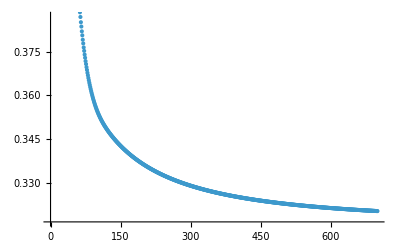

```mathematica
ListPlot[model["EvolutionError"]]
```

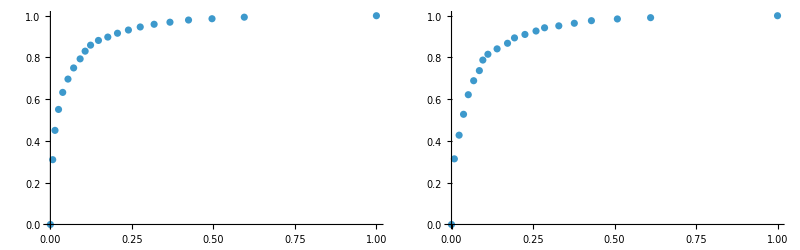

```mathematica
i = 0.5 ;
X1 = traindf[[All, 1]];
Y1 = traindf[[All, 2]];
X2 = testdf[[All, 1]];
Y2 = testdf[[All, 2]];
Y1pred = predictClass[X1, model["weights"], model["bias"]];
Y2pred = predictClass[X2, model["weights"], model["bias"]];


acc1 = accuracy[Y1, Y1pred, i];
acc2 = accuracy[Y2, Y2pred, i];

confMatrix1 = confusionMatrix[Y1, Y1pred, i];
confMatrix1 = {
{"Predit \\ Réel","Positive","Négative"},
{"Positive",confMatrix1["TP"],confMatrix1["FP"]},
{"Négative",confMatrix1["FN"],confMatrix1["TN"]}
};
confMatrix2 = confusionMatrix[Y2, Y2pred, i];
confMatrix2 = {
{"Predit \\ Réel","Positive","Négative"},
{"Positive",confMatrix2["TP"],confMatrix2["FP"]},
{"Négative",confMatrix2["FN"],confMatrix2["TN"]}
};

confMatrix1 = Grid[confMatrix1,Frame->All,Alignment->Center ,Spacings->{2,2},Background->{{LightGray},{LightGray}}];
confMatrix2 = Grid[confMatrix2,Frame->All,Alignment->Center ,Spacings->{2,2},Background->{{LightGray},{LightGray}}];

pre1 = precision[Y1, Y1pred, i];
pre2 = precision[Y2, Y2pred, i];

rec1 = recall[Y1, Y1pred, i];
rec2 = recall[Y2, Y2pred, i];

F1S1 = F1Score[Y1, Y1pred, i];
F1S2 = F1Score[Y2, Y2pred, i];

roc1 = ROCCurve[Y1, Y1pred, 0.05];
roc2 = ROCCurve[Y2, Y2pred, 0.05];


GraphicsGrid[
{
{Style["Données d'entrainement", FontSize->17, FontWeight->Bold], Style["Données de test", FontSize->17, FontWeight->Bold]},
{"ROC curve M1", "ROC curve M2"},
{ListPlot[roc1], ListPlot[roc2]},
{"Matrice de confusion M1", "Matrice de confusion M2"},
{confMatrix1, confMatrix2},
{"\n Accuracy M1",  "\n Accuracy M2"},
{Style[N[acc1], FontSize->14, FontWeight->Bold],  Style[N[acc2], FontSize->14, FontWeight->Bold]}, 
{"\n Précision M1", "\n Précision M2"},
{Style[N[pre1], FontSize->14, FontWeight->Bold],  Style[N[pre2], FontSize->14, FontWeight->Bold]},
{"\n Recall M1", "\n Recall M2"},
{Style[N[rec1], FontSize->14, FontWeight->Bold],  Style[N[rec2], FontSize->14, FontWeight->Bold]}, 
{"\n F1 Score M1", "\n F1 Score M2"},
{Style[N[F1S1], FontSize->14, FontWeight->Bold],  Style[N[F1S2], FontSize->14, FontWeight->Bold]}
}, 
Spacings->{2,5},
Alignment->{Center,Center}
]
```

Ici, nous observons les résultats du modèle entraîné sur un corpus réduit, donc avec peu de mots, mais avec plus de commentaire . Le modèle obtient des résultats cohérents entre les données d’entraînement et de test, ce qui est un bon indicateur de généralisation. L’accuracy reste stable autour de 84–85 %, avec une précision proche de 84 % en entraînement et 83 % en test. Le recall est légèrement plus élevé en test (86.40 %) qu’en entraînement (87.17 %), ce qui montre que le modèle garde une bonne capacité à détecter les classes positives, même hors de l’échantillon d’apprentissage.

Les F1 scores (≈0.86 en entraînement, ≈0.85 en test) confirment cet équilibre. On n’observe pas de surapprentissage ici, contrairement à des modèles plus complexes ou sur-entraînés. Cela  s’expliquer par la taille réduite du vocabulaire  : le modèle apprend plus “généralement” et n’a pas assez d’informations pour trop s’adapter aux données d’entraînement. C’est donc un modèle simple, mais robuste, qui sacrifie un peu de performance brute au profit de la stabilité.

# Utilisation de utilisateur pour faire des prediction

## Fonction de prédiction

```mathematica
mots = nbMotParType3[[All, 1]];
predictUser[texte_, model_, vocabulaire_] := Module[{df, pred}, 
df = {{cleanData[texte], -1}};
df = bagOfWordExtractors[df,vocabulaire];
pred = predictClass[df[[All, 1]], model["weights"], model["bias"]];
Return[pred[[1]]];
]

predictUser["running run plays", model, mots];
```

## Prédiction

```mathematica
DynamicModule[{x="ecrire un commenraire"},
Column[
{
(*Champ de saisie l*)
InputField[Dynamic[x], String, ContinuousAction->True,ImageSize->{1000,60}],

(*Texte affiché avec la couleur sélectionnée*)
Dynamic[
If[predictUser[x, model, mots] >= 0.5, Style["le commentaire est positif", Green, 30], Style["le commentaire est negatif", Red, 30]]
]
}
]
]
```

# Bilan

J’ai choisi ce projet car je voulais experimenter le traitement automatique du langage naturel (NLP) que j’ai appris avec une vidéo Youtube, tout en relevant le défi de recoder entièrement un modèle de régression logistique à partir de zéro. 

Le principal obstacle que j’ai rencontré concernait la grande dimension de mes données textuelles. 
En effet, chaque mot différent génère une nouvelle variable, ce qui fait rapidement exploser le nombre de dimensions, rendant l’apprentissage plus difficile et plus long. 
Pour y remédier, j’ai formulé l’hypothèse que les mots apparaissant avec une fréquence similaire dans les textes positifs et négatifs n’apportaient que peu d’information discriminante.

J’ai donc entraîné deux modèles : un avec l’ensemble des mots, et un autre après avoir filtré les mots considérés comme peu informatifs selon cette hypothèse. 
Les résultats sur les données de test ont confirmé mon intuition, puisque les deux modèles ont obtenu des scores très proches. 
Cela montre que cette réduction de dimension n’a pas affecté la performance, tout en rendant le modèle plus léger et potentiellement plus généralisable.